```mathematica
Clear[RepChromial8];RepChromial8[base_]:=RepChromial8[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,key],x],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
VertexCount[plantri8]
```

17

```mathematica
Clear[RepVect8];RepVect8[base_]:=RepVect8[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->PadRight[CoefficientList[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,key],x],x],20],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
RepVect8["F"]
```

{p1x2x3x4x5→{0,-686808,4062732,-11179006,19059385,-22586469,19749882,-13182082,6843891,-2787401,890524,-221290,41986,-5885,575,-35,1,0,0,0},p12x3x4x5→{0,-1237896,6966864,-18234738,29599778,-33453126,27955422,-17872051,8907470,-3490080,1074783,-257903,47329,-6426,609,-36,1,0,0,0},p13x2x4x5→{0,-1352736,7655136,-20061880,32465420,-36436192,30145255,-19044498,9373125,-3627792,1104828,-262615,47833,-6459,610,-36,1,0,0,0},p14x2x3x5→{0,-1352736,7655136,-20061880,32465420,-36436192,30145255,-19044498,9373125,-3627792,1104828,-262615,47833,-6459,610,-36,1,0,0,0},p15x2x3x4→{0,-1237896,6966864,-18234738,29599778,-33453126,27955422,-17872051,8907470,-3490080,1074783,-257903,47329,-6426,609,-36,1,0,0,0},p1x23x4x5→{0,-1226664,6917184,-18137898,29489670,-33371926,27914698,-17857941,8904126,-3489560,1074735,-257901,47329,-6426,609,-36,1,0,0,0},p1x24x3x5→{0,-1650960,8999328,-22770992,35713584,-39028547,31601276,-19636163,9548689,-3665576,1110579,-263202,47869,-6460,610,-36,1,0,0,0},p1x25x3x4→{0,-1840698,9751185,-24073650,37024460,-39882334,31979143,-19751690,9572858,-3668896,1110850,-263212,47869,-6460,610,-36,1,0,0,0},p1x2x34x5→{0,-1193952,6792256,-17933720,29301716,-33264840,27876035,-17849435,8903182,-3489565,1074748,-257902,47329,-6426,609,-36,1,0,0,0},p1x2x35x4→{0,-1650960,8999328,-22770992,35713584,-39028547,31601276,-19636163,9548689,-3665576,1110579,-263202,47869,-6460,610,-36,1,0,0,0},p1x2x3x45→{0,-1226664,6917184,-18137898,29489670,-33371926,27914698,-17857941,8904126,-3489560,1074735,-257901,47329,-6426,609,-36,1,0,0,0},p123x4x5→{0,-3109608,16673160,-41329658,63215556,-67048300,52430987,-31315054,14573809,-5334586,1536624,-345501,59535,-7607,680,-38,1,0,0,0},p124x3x5→{0,-3808440,20043744,-48676018,72847570,-75560787,57805467,-33817036,15445880,-5562770,1580998,-351748,60139,-7643,681,-38,1,0,0,0},p125x3x4→{0,-3797550,19542303,-46644264,69047422,-71298560,54610085,-32124708,14794382,-5378478,1542868,-346106,59571,-7608,680,-38,1,0,0,0},p12x34x5→{0,-2138436,11570280,-29046469,45170757,-48899612,39166967,-24030591,11513208,-4344298,1290755,-299349,53180,-7000,644,-37,1,0,0,0},p12x35x4→{0,-2920860,15153210,-36488610,54533556,-56908403,44107662,-26299474,12300336,-4550938,1331349,-305155,53753,-7035,645,-37,1,0,0,0},p12x3x45→{0,-2205630,11812203,-29417418,45490632,-49070513,39225065,-24042751,11514541,-4344311,1290742,-299348,53180,-7000,644,-37,1,0,0,0},p134x2x5→{0,-3224496,17508184,-43783764,67265070,-71343248,55573293,-32965179,15208936,-5514977,1574170,-351092,60101,-7642,681,-38,1,0,0,0},p135x2x4→{0,-3808440,20043744,-48676018,72847570,-75560787,57805467,-33817036,15445880,-5562770,1580998,-351748,60139,-7643,681,-38,1,0,0,0},p13x24x5→{0,-3257232,16852364,-40368860,59869947,-61866555,47409120,-27926055,12902305,-4718597,1366103,-310371,54290,-7069,646,-37,1,0,0,0},p13x25x4→{0,-3605004,18143994,-42454628,61822819,-63051177,47898909,-28066578,12930044,-4722214,1366385,-310381,54290,-7069,646,-37,1,0,0,0},p13x2x45→{0,-2387664,12883536,-32179068,49666012,-53243558,42161121,-25549212,12088469,-4507392,1324996,-304531,53716,-7034,645,-37,1,0,0,0},p145x2x3→{0,-3109608,16673160,-41329658,63215556,-67048300,52430987,-31315054,14573809,-5334586,1536624,-345501,59535,-7607,680,-38,1,0,0,0},p14x23x5→{0,-2387664,12883536,-32179068,49666012,-53243558,42161121,-25549212,12088469,-4507392,1324996,-304531,53716,-7034,645,-37,1,0,0,0},p14x25x3→{0,-3605004,18143994,-42454628,61822819,-63051177,47898909,-28066578,12930044,-4722214,1366385,-310381,54290,-7069,646,-37,1,0,0,0},p14x2x35→{0,-3257232,16852364,-40368860,59869947,-61866555,47409120,-27926055,12902305,-4718597,1366103,-310371,54290,-7069,646,-37,1,0,0,0},p15x23x4→{0,-2205630,11812203,-29417418,45490632,-49070513,39225065,-24042751,11514541,-4344311,1290742,-299348,53180,-7000,644,-37,1,0,0,0},p15x24x3→{0,-2920860,15153210,-36488610,54533556,-56908403,44107662,-26299474,12300336,-4550938,1331349,-305155,53753,-7035,645,-37,1,0,0,0},p15x2x34→{0,-2138436,11570280,-29046469,45170757,-48899612,39166967,-24030591,11513208,-4344298,1290755,-299349,53180,-7000,644,-37,1,0,0,0},p1x234x5→{0,-3431832,18124592,-44251322,66710894,-69827815,53983499,-31941019,14757671,-5373677,1542496,-346093,59571,-7608,680,-38,1,0,0,0},p1x235x4→{0,-4680486,23658819,-55325752,80086638,-80788609,60457333,-34789936,15706883,-5613730,1588076,-352413,60177,-7644,681,-38,1,0,0,0},p1x23x45→{0,-2187198,11734647,-29274010,45336131,-48962546,39173706,-24025846,11510727,-4343745,1290692,-299346,53180,-7000,644,-37,1,0,0,0},p1x245x3→{0,-4680486,23658819,-55325752,80086638,-80788609,60457333,-34789936,15706883,-5613730,1588076,-352413,60177,-7644,681,-38,1,0,0,0},p1x24x35→{0,-3926430,19573245,-45308609,65229127,-65768055,49427863,-28689740,13115410,-4762125,1372441,-310994,54327,-7070,646,-37,1,0,0,0},p1x25x34→{0,-3114552,15906922,-37769559,55798112,-57717256,44459896,-26405711,12322330,-4553938,1331593,-305164,53753,-7035,645,-37,1,0,0,0},p1x2x345→{0,-3431832,18124592,-44251322,66710894,-69827815,53983499,-31941019,14757671,-5373677,1542496,-346093,59571,-7608,680,-38,1,0,0,0},p1234x5→{0,-10496700,52833108,-122047091,172887810,-168967051,121293628,-66343952,28246876,-9460575,2496204,-514999,81596,-9607,793,-41,1,0,0,0},p1235x4→{0,-12565422,61007175,-136273986,187450763,-178800631,125934300,-67921007,28637429,-9530809,2505182,-515776,81637,-9608,793,-41,1,0,0,0},p123x45→{0,-5488164,27981870,-65942944,96015655,-97153287,72666658,-41625117,18628233,-6572786,1828992,-398037,66498,-8250,717,-39,1,0,0,0},p1245x3→{0,-12565422,61007175,-136273986,187450763,-178800631,125934300,-67921007,28637429,-9530809,2505182,-515776,81637,-9608,793,-41,1,0,0,0},p124x35→{0,-9002190,43158769,-95533045,130867974,-125033041,88750035,-48536469,20874617,-7126172,1931189,-411804,67780,-8324,719,-39,1,0,0,0},p125x34→{0,-6432780,31850968,-72965149,103551442,-102515152,75346132,-42593945,18884678,-6622298,1835819,-398678,66535,-8251,717,-39,1,0,0,0},p12x345→{0,-6071130,30458379,-70632041,101291177,-101103750,74749552,-42420366,18850229,-6617821,1835474,-398666,66535,-8251,717,-39,1,0,0,0},p1345x2→{0,-10496700,52833108,-122047091,172887810,-168967051,121293628,-66343952,28246876,-9460575,2496204,-514999,81596,-9607,793,-41,1,0,0,0},p134x25→{0,-8431680,40638418,-90592957,125153926,-120667394,86418882,-47641095,20624638,-7075724,1924007,-411120,67741,-8323,719,-39,1,0,0,0},p135x24→{0,-9002190,43158769,-95533045,130867974,-125033041,88750035,-48536469,20874617,-7126172,1931189,-411804,67780,-8324,719,-39,1,0,0,0},p13x245→{0,-9131088,43692556,-96493458,131862156,-125692154,89043844,-48626027,20893118,-7128659,1931386,-411811,67780,-8324,719,-39,1,0,0,0},p145x23→{0,-5488164,27981870,-65942944,96015655,-97153287,72666658,-41625117,18628233,-6572786,1828992,-398037,66498,-8250,717,-39,1,0,0,0},p14x235→{0,-9131088,43692556,-96493458,131862156,-125692154,89043844,-48626027,20893118,-7128659,1931386,-411811,67780,-8324,719,-39,1,0,0,0},p15x234→{0,-6071130,30458379,-70632041,101291177,-101103750,74749552,-42420366,18850229,-6617821,1835474,-398666,66535,-8251,717,-39,1,0,0,0},p1x2345→{0,-13506480,64893384,-143405904,195210646,-184409603,128783741,-68967353,28917867,-9585338,2512692,-516472,81676,-9609,793,-41,1,0,0,0},p12345→{0,-44638752,204166792,-426543264,545509028,-481367651,312348303,-154680663,59730697,-18173424,4361820,-819388,118284,-12693,955,-45,1,0,0,0}}

```mathematica
ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,lambdaKey],x]
```

-10017714 x+48565567 x^2-108512513 x^3+149684021 x^4-143628713 x^5+102117589 x^6-55787628 x^7+23900041 x^8-8103096 x^9+2174117 x^10-457562 x^11+74105 x^12-8930 x^13+755 x^14-40 x^15+x^16

```mathematica
ExpressionToList[allGraphs5[lambdaKey,"colofournull"]//Expand]
```

{p12345/6,p123x45/3,-p124x35/6,p125x34/3,p12x345/3,p12x34x5/6,-p12x35x4/3,p12x3x45/6,-p134x25/6,-p135x24/6,-p13x245/6,p13x24x5/6,p13x25x4/6,-p13x2x45/3,p145x23/3,-p14x235/6,-p14x23x5/3,p14x25x3/6,p14x2x35/6,p15x234/3,p15x23x4/6,-p15x24x3/3,p15x2x34/6,p1x23x45/6,p1x24x35/6,-p1x25x34/3}

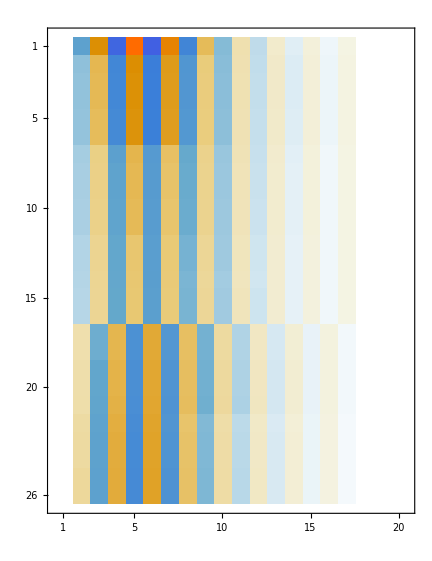

```mathematica
Simplify[ExpressionToList[allGraphs5[lambdaKey,"colofournull"]//Expand]/.RepVect8["F"]]//Sort//MatrixPlot
```

```mathematica
Total[ExpressionToList[allGraphs5[lambdaKey,"colofournull"]//Expand]/.RepVect8["F"]]
```

{0,-10017714,48565567,-108512513,149684021,-143628713,102117589,-55787628,23900041,-8103096,2174117,-457562,74105,-8930,755,-40,1,0,0,0}

```mathematica
allGraphs5[lambdaKey,"colofournull"]/.RepVect8["F"]
```

{0,-10017714,48565567,-108512513,149684021,-143628713,102117589,-55787628,23900041,-8103096,2174117,-457562,74105,-8930,755,-40,1,0,0,0}